```mathematica
thisfolder=NotebookDirectory[];
data=Import[StringJoin[thisfolder,"macula-lc.dat"],"Table"];
dim=Last[Dimensions[data]];
Ns=(dim-6)/3+1;
```

## depiction

### inputs

```mathematica
basics=Flatten[Import[StringJoin[thisfolder,"macula-basics.dat"],"Table"]];
Istar=Extract[basics,1];
j=0;Label[jloop];j=j+1;Subscript[spotfilling, j]=Extract[basics,j+1];If[j<Ns,Goto[jloop]];
"done";
```

### plotting options

```mathematica
size=1.1;
imagesize={200,200};
starstyle=Darker[Gray];
spotthickness=0.004;
latstep=10;
latstyle=Directive[Gray,Opacity[0.5]];
framestyle=White;
lcaspectratio=0.26;
lcimagesize={1200,350};
colortheme="CandyColors";
lcbasestyle={FontFamily->"Helvetica",22,Lighter[Black]};
lcplotstyle=Directive[Lighter[Black],Thickness[0.0018]];
```

### preamble

```mathematica
xrim=Sin[α] Cos[Λx] Cos[φ]+Sin[Λx](Cos[α]Cos[Φx]-Sin[α]Sin[Φx] Sin[φ]);
yrim=Sin[Istar] (Cos[Φx] Sin[α] Sin[φ]+Cos[α] Sin[Φx])+Cos[Istar] (-Cos[α] Cos[Λx] Cos[Φx]+Sin[α] (Cos[φ] Sin[Λx]+Cos[Λx] Sin[φ] Sin[Φx]));
zrim=Cos[Istar] (Cos[Φx] Sin[α] Sin[φ]+Cos[α] Sin[Φx])+Sin[Istar] (Cos[α] Cos[Λx] Cos[Φx]-Sin[α] (Cos[φ] Sin[Λx]+Cos[Λx] Sin[φ] Sin[Φx]));
φcrit=ArcSin[-(Csc[α] (Cos[α] (16 Cos[Λx] Cos[2 Φx] Sin[2 Istar]+(6+10 Cos[2 Istar]+Cos[2 (Istar-Λx)]-2 Cos[2 Λx]+Cos[2 (Istar+Λx)]) Sin[2 Φx]-8 Cos[Λx]^2 Sin[Istar]^2 Sin[2 Φx])-8 √2 Csc[α] √(Sin[Istar]^2 Sin[α]^2 Sin[Λx]^2 (1-4 Cos[2 α]-Cos[2 Λx]+Cos[2 Φx]-Cos[2 Λx] Cos[2 Φx]+Cos[2 Istar] (-1+2 Cos[2 Λx] Cos[Φx]^2+3 Cos[2 Φx])-4 Cos[Λx] Sin[2 Istar] Sin[2 Φx]))))/(20-4 Cos[2 Istar]+2 Cos[2 (Istar-Λx)]-4 Cos[2 Λx]+2 Cos[2 (Istar+Λx)]-4 Cos[2 Istar-Λx-2 Φx]-4 Cos[2 Istar+Λx-2 Φx]+6 Cos[2 (Istar-Φx)]+Cos[2 (Istar-Λx-Φx)]-2 Cos[2 (Λx-Φx)]+Cos[2 (Istar+Λx-Φx)]+4 Cos[2 Φx]+6 Cos[2 (Istar+Φx)]+Cos[2 (Istar-Λx+Φx)]-2 Cos[2 (Λx+Φx)]+Cos[2 (Istar+Λx+Φx)]+4 Cos[2 Istar-Λx+2 Φx]+4 Cos[2 Istar+Λx+2 Φx])];
```

### plot the stargrid

```mathematica
Off[ParametricPlot::plld]
Off[General::plln]
Off[General::indet]
If[Last[QuotientRemainder[Istar*(180/Pi),latstep]]==0,inc=Istar+0.001,inc=Istar];
latitudes=Table[x,{x,-80,80,latstep}];
stargrid=Show[ParametricPlot[{Cos[u],Sin[u]},{u,0,2Pi},Frame->True,PlotRange->{{-size,size},{-size,size}},Axes->None,PlotStyle->starstyle,AspectRatio->1,ImageSize->imagesize,FrameTicks->None,FrameStyle->framestyle],Table[ParametricPlot[{Cos[ϕ] Sin[u],Cos[inc] Cos[u] Cos[ϕ]+Sin[inc] Sin[ϕ]}/.ϕ->(Extract[latitudes,i] (π/180)),{u,-3.14159,-Re[ArcCos[Cot[inc] Tan[Extract[latitudes,i] (π/180)]]]},PlotStyle->latstyle],{i,1,Length[latitudes]}],Table[ParametricPlot[{Cos[ϕ] Sin[u],Cos[inc] Cos[u] Cos[ϕ]+Sin[inc] Sin[ϕ]}/.ϕ->(Extract[latitudes,i] (π/180)),{u,Re[ArcCos[Cot[inc] Tan[Extract[latitudes,i] (π/180)]]],3.14159},PlotStyle->latstyle],{i,1,Length[latitudes]}]];
```

### plot the spots

```mathematica
fselect={40,260,480,697,913};
iselect=Table[Round[N[(Extract[fselect,i]/1000)*Length[data]]],{i,1,Length[fselect]}];
```

```mathematica
l=0;Label[lloop];l=l+1;irow=Extract[iselect,l];row=Extract[data,irow];j=0;Label[rloop];j=j+1;Subscript[Φxval, j]=Extract[row,3+j];Subscript[Λxval, j]=Extract[row,3+Ns+j];Subscript[αval, j]=Extract[row,3+2Ns+j];If[j<Ns,Goto[rloop]];finalgrid={stargrid};j=0;Label[jloop];j=j+1;Subscript[β, j]=ArcCos[Cos[Istar]Sin[Subscript[Φxval, j]]+Sin[Istar]Cos[Subscript[Φxval, j]]Cos[Subscript[Λxval, j]]];spotborderstyle=GrayLevel[1-Subscript[spotfilling, j]];If[Subscript[β, j]>(π/2)+Subscript[αval, j],Subscript[spotplot, j]=finalgrid,If[Subscript[β, j]<(π/2)-Subscript[αval, j],Subscript[spotplot, j]=ParametricPlot[{xrim,yrim}/.Λx->Subscript[Λxval, j]/.Φx->Subscript[Φxval, j]/.α->Subscript[αval, j],{φ,0,2Pi},Mesh->False,BoundaryStyle->None,PerformanceGoal->"Quality"]/.Line[l_List]:>{{ColorData[colortheme][(j-1)/(Ns-1)],Opacity[1-Subscript[spotfilling, j]],Polygon[l]},{spotborderstyle,Line[l]}},If[Subscript[β, j]≤π/2,Subscript[spotplot, j]=Show[ParametricPlot[{xrim,yrim}/.Λx->Subscript[Λxval, j]/.Φx->Subscript[Φxval, j]/.α->Subscript[αval, j],{φ,-Pi,Re[φcrit/.Λx->Subscript[Λxval, j]/.Φx->Subscript[Φxval, j]/.α->Subscript[αval, j]]},Mesh->False,BoundaryStyle->None,PerformanceGoal->"Quality"]/.Line[l_List]:>{{ColorData[colortheme][(j-1)/(Ns-1)],Opacity[1-Subscript[spotfilling, j]],Polygon[l]},{spotborderstyle,Line[l]}},ParametricPlot[{xrim,yrim}/.Λx->Subscript[Λxval, j]/.Φx->Subscript[Φxval, j]/.α->Subscript[αval, j],{φ,-Re[φcrit/.Λx->Subscript[Λxval, j]/.Φx->Subscript[Φxval, j]/.α->Subscript[αval, j]],Pi},Mesh->False,BoundaryStyle->None,PerformanceGoal->"Quality"]/.Line[l_List]:>{{ColorData[colortheme][(j-1)/(Ns-1)],Opacity[1-Subscript[spotfilling, j]],Polygon[l]},{spotborderstyle,Line[l]}}],Subscript[spotplot, j]=Show[ParametricPlot[{xrim,yrim}/.Λx->Subscript[Λxval, j]/.Φx->Subscript[Φxval, j],{φ,Pi+Re[φcrit/.Λx->Subscript[Λxval, j]/.Φx->Subscript[Φxval, j]/.α->Subscript[αval, j]],Pi},{α,0,Subscript[αval, j]},Mesh->False,BoundaryStyle->Black,PerformanceGoal->"Quality",PlotStyle->None],ParametricPlot[{xrim,yrim}/.Λx->Subscript[Λxval, j]/.Φx->Subscript[Φxval, j]/.α->Subscript[αval, j],{φ,-Pi,-Pi-Re[φcrit/.Λx->Subscript[Λxval, j]/.Φx->Subscript[Φxval, j]/.α->Subscript[αval, j]]},{α,0,Subscript[αval, j]},Mesh->False,BoundaryStyle->Black,PerformanceGoal->"Quality",PlotStyle->None]]/.Line[l_List]:>{{ColorData[colortheme][(j-1)/(Ns-1)],Opacity[1-Subscript[spotfilling, j]],Polygon[l]},{ColorData[colortheme][(j-1)/(Ns-1)],Opacity[1-Subscript[spotfilling, j]],Line[l]}}]];finalgrid=Append[finalgrid,Subscript[spotplot, j]]];If[j<Ns,Goto[jloop]];Subscript[final, l]=Show[finalgrid];If[l<Length[fselect],Goto[lloop]];
```

```mathematica
dataselect=Table[{Extract[Extract[data,Extract[iselect,i]],1],Extract[Extract[data,Extract[iselect,i]],2]},{i,1,Length[fselect]}];
datacomp=Import[StringJoin[thisfolder,"macula-lc_components.dat"],"Table"];
j=0;Label[jloop];j=j+1;Subscript[lccomp, j]=datacomp[[All,{1,j+1}]];If[j<Ns,Goto[jloop]];
timeseries=Show[Table[ListPlot[Subscript[lccomp, j],Joined->True,ImageSize->lcimagesize,Frame->True,Joined->True,Axes->None,AspectRatio->lcaspectratio,FrameLabel->{"time [d]",None},BaseStyle->lcbasestyle,PlotRange->All,PlotStyle->Directive[ColorData[colortheme][(j-1)/(Ns-1)],Opacity[0.75]]],{j,1,Ns}],ListPlot[data[[All,{1,2}]],Joined->True,PlotStyle->lcplotstyle],ListPlot[dataselect,PlotMarkers->"×",PlotStyle->Black]];
output=GraphicsColumn[{GraphicsRow[Table[Subscript[final, i],{i,1,Length[fselect]}],Alignment->Left,Spacings->Scaled[0.2]],timeseries},Spacings->Scaled[-0.3]];
```

```mathematica
ddata=Import[StringJoin[thisfolder,"macula-RV.dat"],"Table"];
j=0;Label[jloop];j=j+1;Subscript[rvcomp, j]=ddata[[All,{1,j+1}]];If[j<Ns,Goto[jloop]];
RVt=Table[{Extract[Extract[ddata,i],1],Sum[Extract[Extract[ddata,i],j],{j,2,Ns+1}]},{i,1,Length[ddata]}];
RVtselect=Table[{Extract[Extract[RVt,Extract[iselect,i]],1],Extract[Extract[RVt,Extract[iselect,i]],2]},{i,1,Length[fselect]}];
RVfig=Show[Table[ListPlot[Subscript[rvcomp, j],Joined->True,ImageSize->lcimagesize,Frame->True,Joined->True,Axes->None,AspectRatio->lcaspectratio,FrameLabel->{"time [d]","RV [m/s]"},BaseStyle->lcbasestyle,PlotRange->All,PlotStyle->Directive[ColorData[colortheme][(j-1)/(Ns-1)],Opacity[0.75]]],{j,1,Ns}],ListPlot[RVt[[All,{1,2}]],Joined->True,PlotStyle->lcplotstyle],ListPlot[RVtselect,PlotMarkers->"×",PlotStyle->Black]];
outputx=GraphicsColumn[{output,RVfig},Spacings->Scaled[-0.15]];
```

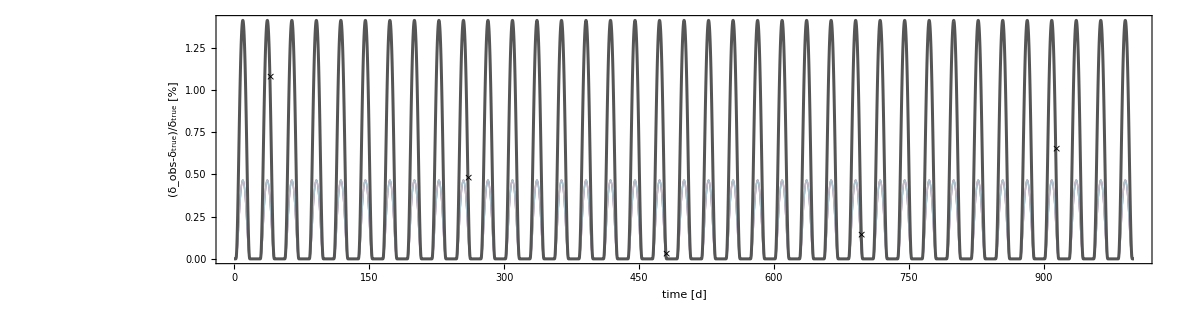

```mathematica
TdeltaV=Table[{Extract[Extract[data,i],1],(Extract[Extract[data,i],3]-1)*100},{i,1,Length[data]}];
dataT=Import[StringJoin[thisfolder,"macula-TdeltaV.dat"],"Table"];
j=0;Label[jloop];j=j+1;Subscript[TdeltaVcomp, j]=Table[{Extract[Extract[dataT,i],1],(Extract[Extract[dataT,i],j+1]-1)*100},{i,1,Length[dataT]}];If[j<Ns,Goto[jloop]];
TdeltaVselect=Table[{Extract[Extract[TdeltaV,Extract[iselect,i]],1],Extract[Extract[TdeltaV,Extract[iselect,i]],2]},{i,1,Length[fselect]}];
TdeltaVfig=Show[Table[ListPlot[Subscript[TdeltaVcomp, j],Joined->True,ImageSize->lcimagesize,Frame->True,Joined->True,Axes->None,AspectRatio->lcaspectratio,FrameLabel->{"time [d]","(δ_obs-δ_true)/δ_true [%]"},BaseStyle->lcbasestyle,PlotRange->All,PlotStyle->Directive[ColorData[colortheme][(j-1)/(Ns-1)],Opacity[0.75]]],{j,1,Ns}],ListPlot[TdeltaV[[All,{1,2}]],Joined->True,PlotStyle->lcplotstyle],ListPlot[TdeltaVselect,PlotMarkers->"×",PlotStyle->Black]];
outputy=GraphicsColumn[{outputx,TdeltaVfig},Spacings->Scaled[-0.5]]
```

```mathematica
Export[StringJoin[thisfolder,"macula-figure.pdf"],outputy]
```

/Users/dkipping/Desktop/macula-plot/macula-figure.pdf